Отчёт по лабораторной работе на тему:
Интерполяция и среднеквадратичное приближение



-Graphics-



f[x_]:=5 Exp[-(1/18 x^2+1/3 x-1/2)]-2 Sin[Sqrt[x]]//N
a=0; b=6; n1=6; n2=10; h1=(b-a)/n1; h2=(b-a)/n2;

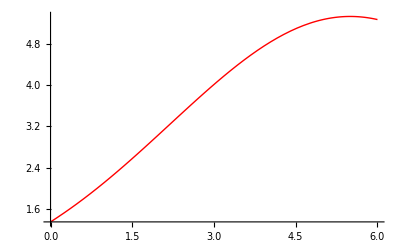

```mathematica
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
points1=Table[{a+i* h1,f[a+i* h1]},{i,0,n1}]//N
points2=Table[{a+i* h2,f[a+i* h2]},{i,0,n2}]//N
Clear[i]
```

{{0.,1.34892},{1.,2.12517},{2.,3.05716},{3.,4.01571},{4.,4.81643},{5.,5.27481},{6.,5.27481}}

{{0.,1.34892},{0.6,1.7913},{1.2,2.30217},{1.8,2.86347},{2.4,3.44694},{3.,4.01571},{3.6,4.52771},{4.2,4.94061},{4.8,5.21758},{5.4,5.33267},{6.,5.27481}}

```mathematica
PLn1[x_]=∏_(i=0)^n1 (x-points1[[i+1,1]])
PLn2[x_]=∏_(i=0)^n2 (x-points2[[i+1,1]])|
Clear[i]
```

(-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x) (0.+x)

(-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)|Null

```mathematica
Ln1[x_]=Sum[points1[[i+1,2]] PLn1[x]/((x-points1[[i+1,1]]) PLn1'[points1[[i+1,1]]]),{i,0,n1}]//Simplify
Ln2[x_]=Sum[points2[[i+1,2]] PLn2[x]/((x-points2[[i+1,1]]) PLn2'[points2[[i+1,1]]]),{i,0,n2}]//Simplify
Clear[i]
```

1.34892+0.677865 x+0.0993773 x^2+0.00410019 x^3-0.0052918 x^4+0.000177097 x^5+0.0000187873 x^6

((1.34892+0.674466 x+0.10728 x^2-0.00251663 x^3-0.00279565 x^4-0.000207773 x^5+0.0000155243 x^6+5.74302×10^-6 x^7+6.27748×10^-8 x^8-9.22089×10^-8 x^9+4.81649×10^-9 x^10) ((-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)|Null))/((-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x) Alternatives^(1,0)[0.,Null])

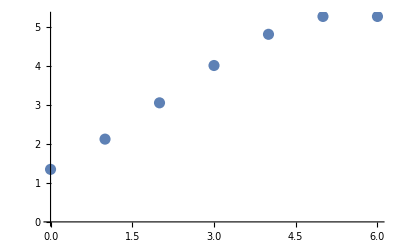

```mathematica
graphF1=ListPlot[points1,PlotStyle->{Darker,PointSize[0.02]}]
```

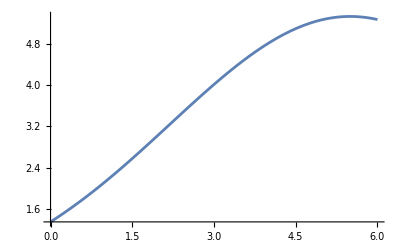

```mathematica
graphLn1=Plot[Ln1[x],{x,a,b}]
```

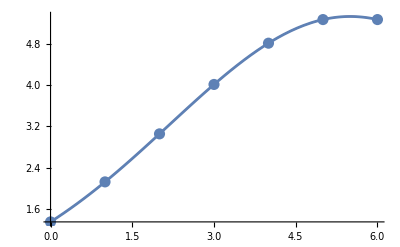

```mathematica
Show[graph,graphF1,graphLn1]
```

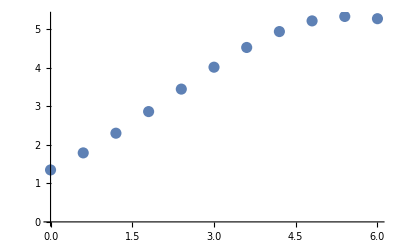

```mathematica
graphF2=ListPlot[points2,PlotStyle->{Darker,PointSize[0.02]}]
```

```mathematica
graphLn2=Plot[Ln2[x],{x,a,b}];
```

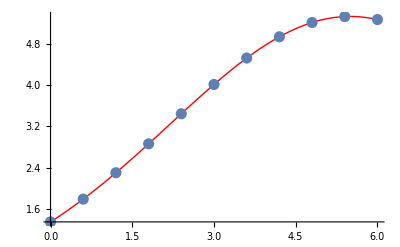

```mathematica
Show[graph,graphF2,graphLn2]
```

```mathematica
TableDif1= Table[0,{i,0,n1},{j,0,n1}];
For[i=1,i<=n1+1,i++,For[j=1,j<=n1+1,j++,If[(i+j)>n1+2,TableDif1[[i,j]]=""];]];
For[i=1,i<=n1+1,i++,TableDif1[[i,1]]=points1[[i,2]]]
For[j=2,j<=n1+1,j++,
For[i=1,i<=n1+2-j,i++,
TableDif1[[i,j]]=TableDif1[[i+1,j-1]]-TableDif1[[i,j-1]]]];
MatrixForm[TableDif1]
Clear[i,j]
```

(1.34892 | 0.776247 | 0.155748 | -0.129194 | -0.0551918 | 0.0550687 | 0.0135268
2.12517 | 0.931995 | 0.0265542 | -0.184386 | -0.000123106 | 0.0685956 | 
3.05716 | 0.958549 | -0.157832 | -0.184509 | 0.0684725 |  | 
4.01571 | 0.800718 | -0.342341 | -0.116037 |  |  | 
4.81643 | 0.458377 | -0.458377 |  |  |  | 
5.27481 | 0. |  |  |  |  | 
5.27481 |  |  |  |  |  | )

```mathematica
TableDif2= Table[0,{i,0,n2},{j,0,n2}];
For[i=1,i<=n2+1,i++,For[j=1,j<=n2+1,j++,If[(i+j)>n2+2,TableDif2[[i,j]]=""];]];
For[i=1,i<=n2+1,i++,TableDif2[[i,1]]=points2[[i,2]]]
For[j=2,j<=n2+1,j++,
For[i=1,i<=n2+2-j,i++,
TableDif2[[i,j]]=TableDif2[[i+1,j-1]]-TableDif2[[i,j-1]]]];
MatrixForm[TableDif2]
Clear[i,j]
```

(1.34892 | 0.442379 | 0.068488 | -0.018056 | -0.0101992 | 0.00157223 | 0.00186256 | -0.000341604 | -0.000425624 | 0.000138367 | 0.000105683
1.7913 | 0.510867 | 0.050432 | -0.0282552 | -0.00862693 | 0.00343479 | 0.00152096 | -0.000767228 | -0.000287256 | 0.00024405 | 
2.30217 | 0.561299 | 0.0221768 | -0.0368821 | -0.00519214 | 0.00495575 | 0.000753728 | -0.00105448 | -0.0000432061 |  | 
2.86347 | 0.583476 | -0.0147053 | -0.0420743 | -0.000236395 | 0.00570948 | -0.000300756 | -0.00109769 |  |  | 
3.44694 | 0.568771 | -0.0567796 | -0.0423107 | 0.00547308 | 0.00540872 | -0.00139845 |  |  |  | 
4.01571 | 0.511991 | -0.0990903 | -0.0368376 | 0.0108818 | 0.00401027 |  |  |  |  | 
4.52771 | 0.412901 | -0.135928 | -0.0259558 | 0.0148921 |  |  |  |  |  | 
4.94061 | 0.276973 | -0.161884 | -0.0110637 |  |  |  |  |  |  | 
5.21758 | 0.115089 | -0.172947 |  |  |  |  |  |  |  | 
5.33267 | -0.0578584 |  |  |  |  |  |  |  |  | 
5.27481 |  |  |  |  |  |  |  |  |  | )

```mathematica
q1[x_]=(x-points1[[n1+1,1]])/h1;
q2[x_]=(x-points2[[n2+1,1]])/h2;
```

```mathematica
P1[x_]=Sum[(TableDif1[[n1+1-p,p+1]]/Factorial[p])*∏_(k=1)^p (q1[x]+k-1),{p,0,n1}]//Simplify
P2[x_]=Sum[(TableDif2[[n2+1-p,p+1]]/Factorial[p])*∏_(k=1)^p (q2[x]+k-1),{p,0,n2}]//Simplify
```

1.34892+0.677865 x+0.0993773 x^2+0.00410019 x^3-0.0052918 x^4+0.000177097 x^5+0.0000187873 x^6

1.34892+0.674466 x+0.10728 x^2-0.00251663 x^3-0.00279565 x^4-0.000207773 x^5+0.0000155243 x^6+5.74302×10^-6 x^7+6.27748×10^-8 x^8-9.22089×10^-8 x^9+4.81649×10^-9 x^10

```mathematica
graphP1=Plot[P1[x],{x,a,b}]
```

-Graphics-

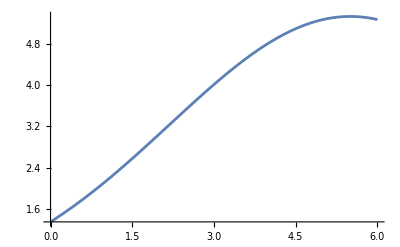

```mathematica
graphP2=Plot[P2[x],{x,a,b}]
```

```mathematica
NP1[x_]=InterpolatingPolynomial[points1,x];NP2[x_]=InterpolatingPolynomial[points2,x];
```

```mathematica
graphNP1=Plot[NP1[x],{x,a,b}]
```

-Graphics-

```mathematica
Set[graphNP1,Plot[NP1[x],{x,a,b}]]
```

-Graphics-

```mathematica
graphNP2=Plot[NP2[x],{x,a,b}]
```

-Graphics-

```mathematica
x1=2.4316;
Ln1[x1]
Ln2[x1]
P1[x1]
P2[x1]
NP1[x1]
NP2[x1]
Clear[x1]
```

3.47769

(1.07816 (3.22551|Null))/(Alternatives^(1,0)[0.,Null])

3.47769

3.47762

3.47769

3.47762

```mathematica
R1[x_]=Abs[f[x]-NP1[x]];
R2[x_]=Abs[f[x]-NP2[x]];
```

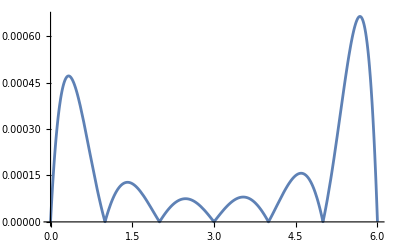

```mathematica
graphR1=Plot[R1[x],{x,a,b}]
```

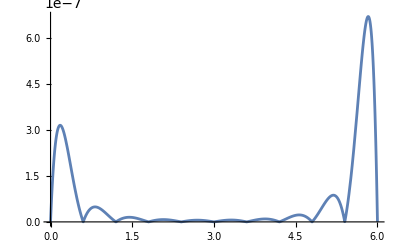

```mathematica
graphR2=Plot[R2[x],{x,a,b},PlotRange->{{0,6},{0,0.00000067}}]
```

```mathematica
FindMaximum[R1[x],{x,0,5}]
FindMaximum[R2[x],{x,0,6}]
Clear[points1,points2,TableDif1,TableDif2]
```

{0.000471242,{x→0.331536}}

{3.15084×10^-7,{x→0.175193}}

```mathematica
t[i_,n_]=Cos[Pi*(2*i+1)/(2n+2)]
```

Cos[1/22 (1+2 i) π]
-Graphics-

```mathematica
points1=Table[{((a+b)/2)+((b-a)/2)*t[i,n1],f[((a+b)/2)+((b-a)/2)*t[i,n1]]},{i,0,n1}]//N
points2=Table[{((a+b)/2)+((b-a)/2)*t[i,n2],f[((a+b)/2)+((b-a)/2)*t[i,n2]]},{i,0,n2}]//N
```

{{5.96946,5.28191},{5.7289,5.3224},{5.26725,5.32197},{4.62192,5.15135},{3.8452,4.71069},{3.,4.01571},{2.1548,3.20802}}

{{5.96946,5.28191},{5.7289,5.3224},{5.26725,5.32197},{4.62192,5.15135},{3.8452,4.71069},{3.,4.01571},{2.1548,3.20802},{1.37808,2.46458},{0.732751,1.8989},{0.271104,1.53959},{0.0305357,1.36962}}

```mathematica
TableDif1= Table[0,{i,0,n1},{j,0,n1}];
For[i=1,i<=n1+1,i++,For[j=1,j<=n1+1,j++,If[(i+j)>n1+2,TableDif1[[i,j]]=""];]];
For[i=1,i<=n1+1,i++,TableDif1[[i,1]]=points1[[i,2]]];
For[j=2,j<=n1+1,j++,
For[i=1,i<=n1+2-j,i++,
TableDif1[[i,j]]=(TableDif1[[i+1,j-1]]-TableDif1[[i,j-1]])/(points1[[i+j-1,1]]-points1[[i,1]])]];
MatrixForm[TableDif1]
Clear[i,j]
```

(5.28191 | -0.168309 | -0.241011 | -0.00223777 | 0.00518418 | 0.000340687 | -0.0000495439
5.3224 | 0.000932663 | -0.237995 | -0.0132503 | 0.00417252 | 0.000529681 | 
5.32197 | 0.264387 | -0.213036 | -0.0246367 | 0.00227939 |  | 
5.15135 | 0.567335 | -0.157178 | -0.0317312 |  |  | 
4.71069 | 0.822266 | -0.0788936 |  |  |  | 
4.01571 | 0.955627 |  |  |  |  | 
3.20802 |  |  |  |  |  | )

```mathematica
TableDif2= Table[0,{i,0,n2},{j,0,n2}];
For[i=1,i<=n2+1,i++,For[j=1,j<=n2+1,j++,If[(i+j)>n2+2,TableDif2[[i,j]]=""];]];
For[i=1,i<=n2+1,i++,TableDif2[[i,1]]=points2[[i,2]]];
For[j=2,j<=n2+1,j++,
For[i=1,i<=n2+2-j,i++,
TableDif2[[i,j]]=(TableDif2[[i+1,j-1]]-TableDif2[[i,j-1]])/(points2[[i+j-1,1]]-points2[[i,1]])]];
MatrixForm[TableDif2]
Clear[i,j]
```

(5.28191 | -0.168309 | -0.241011 | -0.00223777 | 0.00518418 | 0.000340687 | -0.0000495439 | -7.44175×10^-6 | -3.22923×10^-8 | 6.43486×10^-8 | 4.60901×10^-9
5.3224 | 0.000932663 | -0.237995 | -0.0132503 | 0.00417252 | 0.000529681 | -0.0000153759 | -7.27265×10^-6 | -3.98974×10^-7 | 3.6976×10^-8 | 
5.32197 | 0.264387 | -0.213036 | -0.0246367 | 0.00227939 | 0.000596578 | 0.0000209593 | -5.09513×10^-6 | -6.09676×10^-7 |  | 
5.15135 | 0.567335 | -0.157178 | -0.0317312 | -0.0000408049 | 0.000501538 | 0.0000464153 | -1.90243×10^-6 |  |  | 
4.71069 | 0.822266 | -0.0788936 | -0.0315988 | -0.00199137 | 0.000299594 | 0.0000551501 |  |  |  | 
4.01571 | 0.955627 | -0.00093548 | -0.0254008 | -0.00306215 | 0.000089215 |  |  |  |  | 
3.20802 | 0.957145 | 0.0566544 | -0.0170445 | -0.00332707 |  |  |  |  |  | 
2.46458 | 0.876579 | 0.0887611 | -0.00997691 |  |  |  |  |  |  | 
1.8989 | 0.778323 | 0.102205 |  |  |  |  |  |  |  | 
1.53959 | 0.706553 |  |  |  |  |  |  |  |  | 
1.36962 |  |  |  |  |  |  |  |  |  | )

```mathematica
P1[x_]=Sum[(TableDif1[[1,p]])*∏_(k=1)^(p-1) (x-points1[[k,1]]),{p,1,n1+1}]//Simplify
P2[x_]=Sum[(TableDif2[[1,p]])*∏_(k=1)^(p-1) (x-points2[[k,1]]),{p,1,n2+1}]//Simplify
```

1.19716+0.945187 x-0.0923954 x^2+0.0757776 x^3-0.0200051 x^4+0.00174935 x^5-0.0000495439 x^6

```mathematica
1.3489224911292106+0.6744626314213413 x+0.10729178502073082 x^2-0.002532950663635635 x^3-0.0027845587978359452 x^4-0.00021154096149478206 x^5+0.000015986956353261102 x^6+5.828073897837489*^-6 x^7+2.636183745811167*^-8 x^8-8.760806540560899*^-8 x^9+4.609012356339063*^-9 x^10
-Graphics-
```

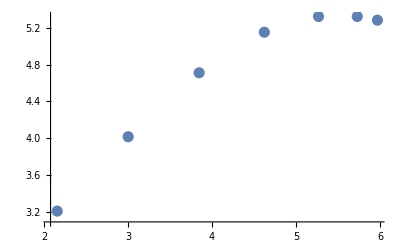

```mathematica
graphF1=ListPlot[points1,PlotStyle->{Darker,PointSize[0.02]}]
```

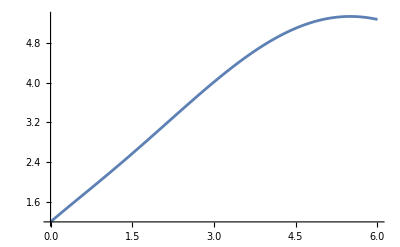

```mathematica
graphP1=Plot[P1[x],{x,a,b}]
```

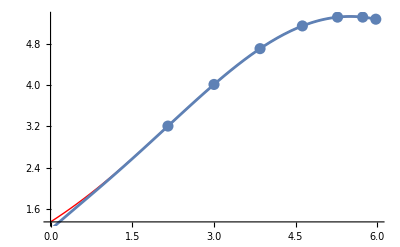

```mathematica
Show[graph,graphF1,graphP1]
```

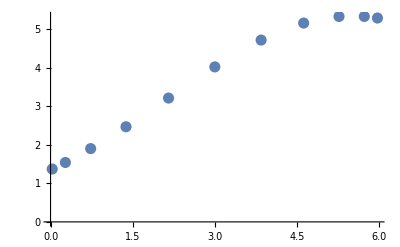

```mathematica
graphF2=ListPlot[points2,PlotStyle->{Darker,PointSize[0.02]}]
```

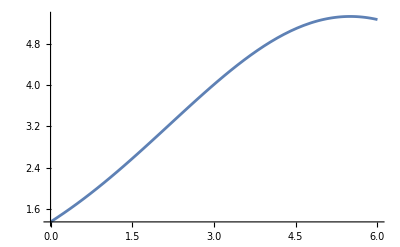

```mathematica
graphP2=Plot[P2[x],{x,a,b}]
```

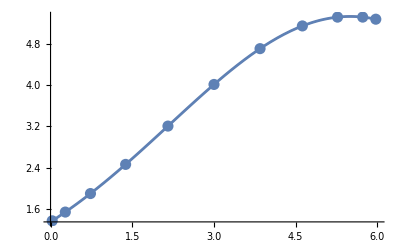

```mathematica
Show[graph,graphF2,graphP2]
```

```mathematica
IntF1=Interpolation[points1];
IntF2=Interpolation[points2];
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

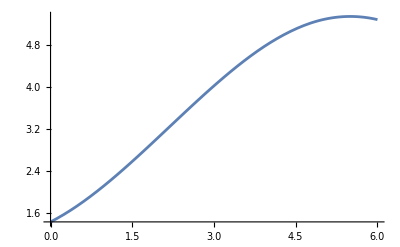

```mathematica
graphIntF1=Plot[IntF1[x],{x,a,b}]
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

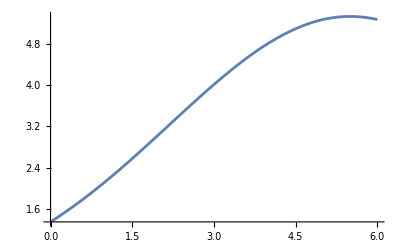

```mathematica
graphIntF2=Plot[IntF2[x],{x,a,b}]
```

```mathematica
x1=2.4316;
P1[x1]
P2[x1]
IntF1[x1]
IntF2[x1]
```

3.47774

3.47762

3.47789

3.47792

```mathematica
RnP1[x_]=Abs[f[x]-P1[x]];//Simplify
```

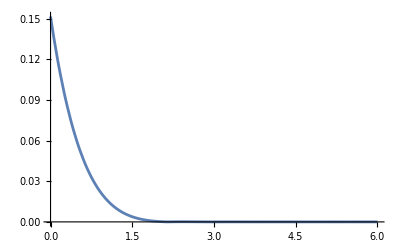

```mathematica
graphErrp1=Plot[RnP1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrP1=FindMaximum[{RnP1[x],0<=x<=6},x]
```

{0.151766,{x→3.25748×10^-7}}

```mathematica
RnIntF1[x_]=Abs[f[x]-IntF1[x]]//Simplify;
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

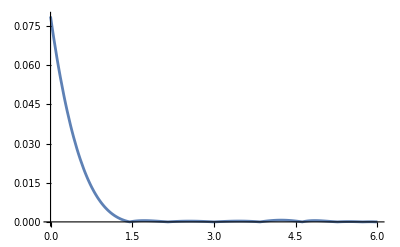

```mathematica
graphErrI1=Plot[RnIntF1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrIntF1=FindMaximum[{RnIntF1[x],0<=x<=6},x]
```

InterpolatingFunction::dmval: Input value {0.599994} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.600006} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.599994} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.0786489,{x→6.11543×10^-7}}

```mathematica
f[x_]:=Sqrt[3]*Exp[-x^2/22+x/2-1/4]//N
a=0; b=6; n=10; h=(b-a)/n;
points=Table[{a+i* h,f[a+i* h]},{i,0,n}]//N
```

{{0.,1.34892},{0.6,1.7913},{1.2,2.30217},{1.8,2.86347},{2.4,3.44694},{3.,4.01571},{3.6,4.52771},{4.2,4.94061},{4.8,5.21758},{5.4,5.33267},{6.,5.27481}}

```mathematica
listC=Table[0,{k,0,n}];
Matrix=Table[0,{n-1},{n-1}];
Do[
If[i≠1,Matrix[[i,i-1]]=h];Matrix[[i,i]]=4 h;If[i≠n-1,Matrix[[i,i+1]]=h],{i,1,n-1}];
Matrix//MatrixForm//N
B=Table[3 ((points[[i,2]]-points[[i-1,2]])/h-(points[[i-1,2]]-points[[i-2,2]])/h),{i,3,n+1}]//N;
B//MatrixForm//N
```

(2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4)

(0.34244
0.25216
0.110884
-0.0735267
-0.283898
-0.495452
-0.679639
-0.809418
-0.864737)

```mathematica
X=LinearSolve[Matrix,B];
For[i=1,i<=n-1,i++,
listC[[i+1]]=X[[i]]]
MatrixForm[listC]
```

(0
0.126507
0.0647068
0.0349328
-0.0196315
-0.0789515
-0.137726
-0.195896
-0.211421
-0.307452
0)

```mathematica
listA=Table[0,{i,1,n}];
listB=Table[0,{i,1,n}];
listD=Table[0,{i,1,n}];
For[i=1,i<=n,i++,
listA[[i]]=points[[i+1,2]]]
For[i=1,i<=n,i++,
listB[[i]]=(points[[i+1,2]]-points[[i,2]])/h+2/3*h*listC[[i+1]]+1/3*h*listC[[i]]]
For[i=1,i<=n,i++,
listD[[i]]=(listC[[i+1]]-listC[[i]])/(3h)]
G=Table[{listA[[i]]+listB[[i]](x-points[[i+1,1]])+listC[[i+1]](x-points[[i+1,1]])^2+listD[[i]](x-points[[i+1,1]])^3,points[[i,1]]<=x<=points[[i+1,1]]},{i,1,n}];//Simplify
```

```mathematica
S[x_]=Piecewise[G]
```

```mathematica
Piecewise[{{1.7913016027332511+0.7879011486388656 (-0.6+x)+0.1265067154340377 (-0.6+x)^2+0.07028150857446538 (-0.6+x)^3, 0.≤x≤0.6}, {2.3021687164931626+0.9026292422614036 (-1.2+x)+0.06470677393685895 (-1.2+x)^2-0.034333300831765966 (-1.2+x)^3, 0.6≤x≤1.2}, {2.8634678264948015+0.962413001123272 (-1.8+x)+0.03493282416625509 (-1.8+x)^2-0.016541083205891035 (-1.8+x)^3, 1.2≤x≤1.8}, {3.4469437281193267+0.971593811376329 (-2.4+x)-0.019631473744493404 (-2.4+x)^2-0.030313498839304717 (-2.4+x)^3, 1.8≤x≤2.4}, {4.015714283224617+0.9124440370204902 (-3.+x)-0.078951483515238 (-3.+x)^2-0.032955560983746995 (-3.+x)^3, 2.4≤x≤3.}, {4.527705211178085+0.7824374558355016 (-3.6+x)-0.1377261517930764 (-3.6+x)^2-0.03265259348768801 (-3.6+x)^3, 3.≤x≤3.6}, {4.940605835847711+0.5822639027529719 (-4.2+x)-0.1958964366778063 (-4.2+x)^2-0.03231682493596105 (-4.2+x)^3, 3.6≤x≤4.2}, {5.217578560969526+0.33787368210981833 (-4.8+x)-0.21142059772744984 (-4.8+x)^2-0.008624533916468637 (-4.8+x)^3, 4.2≤x≤4.8}, {5.332667589863274+0.026550138885569133 (-5.4+x)-0.30745197431296545 (-5.4+x)^2-0.0533507647697309 (-5.4+x)^3, 4.8≤x≤5.4}, {5.274809199359503-0.15792104570221005 (-6.+x)+0.1708066523960919 (-6.+x)^3, 5.4≤x≤6.}, {0, True}}]
-Graphics-
```

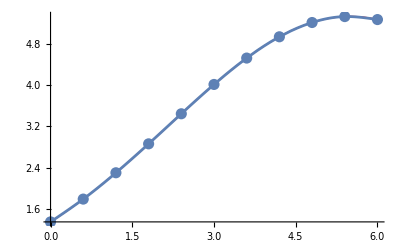

```mathematica
graphF=ListPlot[points,PlotStyle->{Darker,PointSize[0.02]}];
graphS=Plot[S[x],{x,a,b}];
Show[graph,graphF,graphS]
```

```mathematica
Sf[x_]=Interpolation[points,x,Method->"Spline"];
```

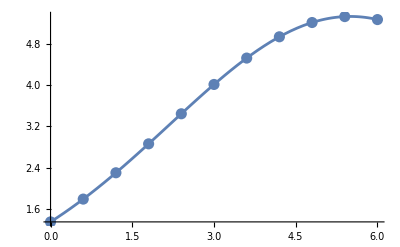

```mathematica
graphSf=Plot[Sf[x],{x,a,b}];
Show[graphSf,graphF]
```

```mathematica
Needs["Splines`"]
```

```mathematica
Spl=SplineFit[points,Cubic];
```

```mathematica
t[x]=(x-a)/h;
graphSpl=ParametricPlot[Spl[t],{t,0,n}];
```

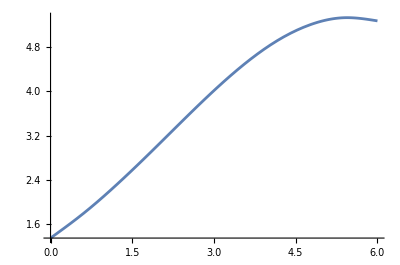

```mathematica
Show[graphSpl]
```

```mathematica
x1=2.4316;
S[x1]
Sf[x1]
Last[Spl[(x1-a)/h]]
```

3.47763

3.47762

3.47763

```mathematica
m1=1;
SummaA[k_,l_]:=If[(k+l)!=2,Sum[(points[[t+1,1]])^(k+l-2),{t,0,n}],Sum[1,{t,0,n}]]
```

```mathematica
listA1=Table[SummaA[i,j],{i,1,m1+1},{j,1,m1+1}];//N
MatrixForm[listA1]
```

(11 | 33.
33. | 138.6)

```mathematica
SummaB[k_]:=If[k!=1,Sum[points[[t+1,2]]*((points[[t+1,1]])^(k-1)),{t,0,n}],Sum[points[[t+1,2]],{t,0,n}]]
```

```mathematica
listB1=Table[SummaB[i],{i,1,m1+1}];//N
MatrixForm[listB1]
```

```mathematica
({{41.061885079537355}, {151.85135385115655}})
-Graphics-
```

```mathematica
A1=LinearSolve[listA1,listB1]
```

{1.56125,0.723881}

```mathematica
Q1[x_]=Sum[A1[[t+1]]*x^(t),{t,0,m1}]
graphQ1=Plot[Q1[x],{x,a,b},PlotStyle->Blue];
Show[graphF2,graphQ1]
```

```mathematica
1.5612548093106313+0.7238812780945578 x
```

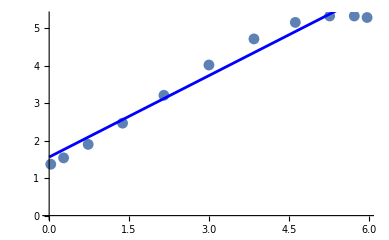

(11 | 33. | 138.6
33. | 138.6 | 653.4
138.6 | 653.4 | 3283.16)

(41.0619
151.851
680.672)

1.13864+1.19345 x-0.0782614 x^2

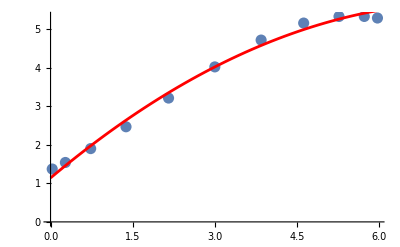

```mathematica
m2=2;
listA2=Table[SummaA[i,j],{i,1,m2+1},{j,1,m2+1}];//N
MatrixForm[listA2]
listB2=Table[SummaB[i],{i,1,m2+1}];//N
MatrixForm[listB2]
A2=LinearSolve[listA2,listB2];
Q2[x_]=Sum[A2[[t+1]]*x^(t),{t,0,m2}]
graphQ2=Plot[Q2[x],{x,a,b},PlotStyle->Red];
Show[graphF2,graphQ2]
```

1.35204+0.628349 x+0.168723 x^2-0.0274427 x^3

1.35348+0.619984 x+0.175694 x^2-0.0293016 x^3+0.000154904 x^4

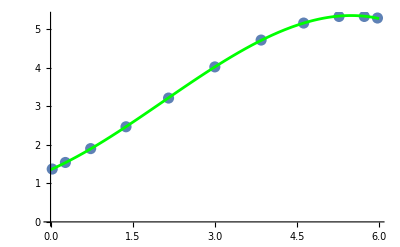

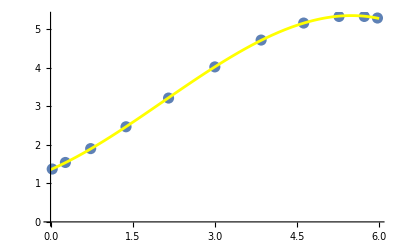

```mathematica
Q3[x_]=Fit[points,{1,x,x^2,x^3},x]
Q4[x_]=Fit[points,{1,x,x^2,x^3,x^4},x]
graphQ3=Plot[Q3[x],{x,a,b},PlotStyle->Green];
graphQ4=Plot[Q4[x],{x,a,b},PlotStyle->Yellow];
Show[graphF2,graphQ3]
Show[graphF2,graphQ4]
```

```mathematica
x1=2.4316;
f[x1]
Q1[x1]
Q2[x1]
Q3[x1]
Q4[x1]
```

3.47762

3.32144

3.5779

3.48299

3.484

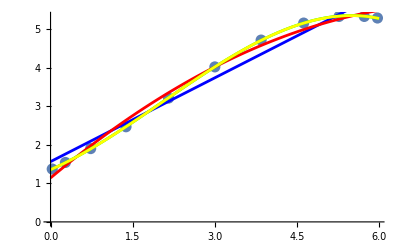

```mathematica
Show[graphF2,graphQ1,graphQ2,graphQ3,graphQ4]
```